```mathematica
SetDirectory[NotebookDirectory[]<>"../Data"];

LAhydroParametersImport=Import["USGS_gage_hydro_variables_lwi-transition-zone.csv"]; (*lwi-transition-zone jacksonville*)
LAmodelParametersImport=Import["LWI_output.csv"]; 


FLhydroParametersImport=Import["USGS_gage_hydro_variables_jacksonville.csv"]; (*lwi-transition-zone jacksonville*)
FLmodelParametersImport=Import["Jacksonville_output.csv"];
```

```mathematica
FLmodelParametersImport[[All,8]]
Drop[FLhydroParametersImport[[All,4]],1]
```

{NSE,0.926639,0.938871,0.90806,0.958315,0.957932,0.982472,0.875586,0.982459,0.975787,0.931483,0.938136,0.991332,0.990473,0.990227,0.865389,0.995666,0.870473,0.934458,0.978588,0.986447,0.962033,0.986715,0.989828,0.973757,0.882322,0.934903,0.860394,0.99277,0.915412,0.973144,0.995337,0.935424,0.967984,0.988342,0.84878,0.991328,0.991163,0.981671,0.986643,0.974874,0.872054,0.962429,0.989118,0.94924,0.99534,0.993466,0.994527,0.951437,0.954354,0.987632,0.958693,0.993889,0.979633,0.915993,0.984252,0.984252}

{0.920914,0.902132,0.922792,0.683217,0.477875,0.891312,0.870634,0.809327,0.797138,0.816623,0.677889,0.826369,0.784956,0.706954,0.788415,0.776383,0.64159,0.502402,0.605369,0.797168,0.751458,0.799825,0.673587,0.561937,0.66408,0.287818,0.84535,0.94147,0.652203,0.620601,0.562773,0.670174,0.667283,0.821317,0.892367,0.766539,0.80126,0.855372,0.869604,0.740985,0.511019,0.791495,0.758387,0.899974,0.741067,0.766144,0.719557,0.690138,0.565714,0.624435,0.343978,0.390686,0.353286,0.491313,0.746313,0.787873}

```mathematica
ETRobsFlorida =Drop[FLhydroParametersImport[[All,4]],1];
ETRobsLWI =Drop[LAhydroParametersImport[[All,4]],1];

FloridaQfQb = Drop[FLhydroParametersImport[[All,5]],1];
LWIQfQb =Drop[LAhydroParametersImport[[All,5]],1];

FloridaNSE = Drop[FLmodelParametersImport[[All,8]],1];
LWINSE =  Drop[LAmodelParametersImport[[All,8]],1];
```

14

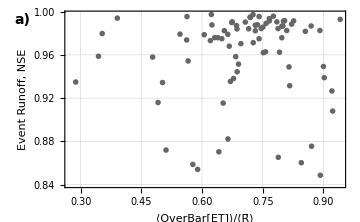

```mathematica
Textsize =14
data=Transpose[{ETRobsFlorida ~Join~ETRobsLWI,FloridaNSE ~Join~LWINSE  }];
part11 = ListPlot[data,PlotMarkers->Graphics[{Thickness[0.01],Circle[{0,0},Scaled[0.01]]}],PlotStyle->{GrayLevel[.4]},Frame->{{True,False},{True,False}},ImageSize->Medium,PlotTheme->"Detailed",Frame->{{True,False},{True,False}},FrameLabel->{{"Event Runoff, NSE",None},{Style["⟨OverBar[ET]⟩/⟨R̄⟩",16], None}},LabelStyle->Directive[Textsize  ,Bold],PlotRangeClipping->False];
labeledPlot[fig_,label_]:=Show[fig,Graphics[{Text[Style[label,Bold,14],Scaled[{-0.15,.95}]]}]]
panel1=labeledPlot[part11,"a)"]
```

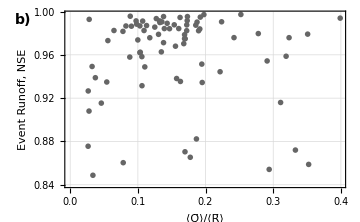

```mathematica
data=Transpose[{(1-(ETRobsFlorida ~Join~ETRobsLWI ))(1-(FloridaQfQb ~Join~LWIQfQb )) ,FloridaNSE ~Join~LWINSE  }];
part22 = ListPlot[data,PlotMarkers->Graphics[{Thickness[0.01],Circle[{0,0},Scaled[0.01]]}],PlotStyle->{GrayLevel[.4]},Frame->{{True,False},{True,False}},ImageSize->Medium,PlotTheme->"Detailed",Frame->{{True,False},{True,False}},FrameLabel->{{"Event Runoff, NSE",None},{Style["⟨Q̄⟩/⟨R̄⟩",16], None}},LabelStyle->Directive[Textsize  ,Bold],PlotRangeClipping->False];
labeledPlot[fig_,label_]:=Show[fig,Graphics[{Text[Style[label,Bold,14],Scaled[{-0.15,.95}]]}]]
panel2=labeledPlot[part22,"b)"]
```

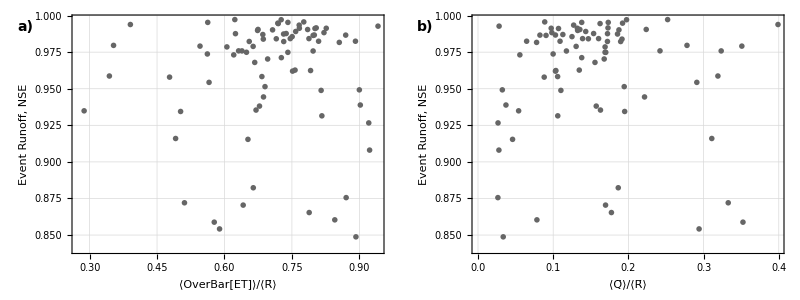

```mathematica
grid1=Grid[{{panel1,panel2}},Spacings->{2,1}]
```

```mathematica
SetDirectory[NotebookDirectory[]<>"../Data"];
Export["Figure9.pdf",grid1]
```

Figure9.pdf

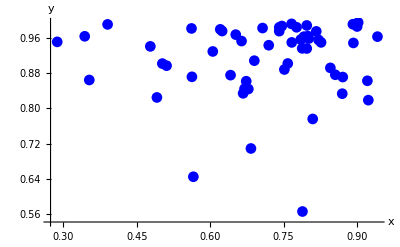

```mathematica
data=Transpose[{ETRobsFlorida,FloridaNSE  }];
ListPlot[data,AxesLabel->{"x","y"},PlotStyle->Blue,PlotMarkers->Automatic]
```

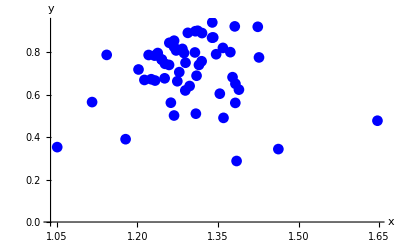

```mathematica
data=Transpose[{FloridaDI , ETRobsFlorida}];
ListPlot[data,AxesLabel->{"x","y"},PlotStyle->Blue,PlotMarkers->Automatic]
```

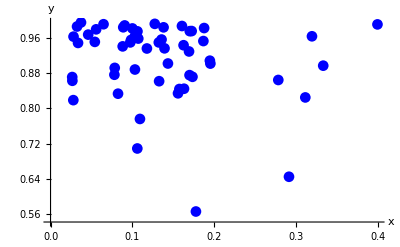

```mathematica
data=Transpose[{(1-ETRobsFlorida )(1-FloridaQfQb) ,FloridaNSE   }];
ListPlot[data,AxesLabel->{"x","y"},PlotStyle->Blue,PlotMarkers->Automatic]
```